## Weighted Fit

```mathematica
data={{1,0.8426871299743652},{2,0.8406062126159668},{1,3.226578116416931},{2,3.2243930101394653},{1,7.174222350120544},{2,7.171901345252991},{1,12.689524383982643},{2,12.686958156293258},{1,19.773917039623484},{2,19.770949750440195},{1,28.428132182219997},{2,28.42456082510762},{1,38.652617557672784},{2,38.64820022252388},{1,50.44768833811395},{2,50.44213713775389},{1,63.81358461291529},{2,63.80656921979971},{1,78.75050342851318},{2,78.74164824537002},{1,95.25861514895223},{2,95.2474993087817},{1,113.3380695336964},{2,113.32422760711052},{1,132.98900753981434},{2,132.97192529099993},{1,154.2115601298865},{2,154.1906752239447},{1,177.00585263001267},{2,176.98055447207298},{1,201.3720079708146},{2,201.34163383964915},{1,227.31014622107614},{2,227.2739820581628},{1,254.8203860449139},{2,254.7776627393905},{1,283.90284618304577},{2,283.85273952421267},{1,314.5576463358011},{2,314.4992729885271},{1,346.7849062484456},{2,346.717324694735},{1,380.58474809338804},{2,380.5069524239516}};
```

This data is from parallelsperiment_mod -- I just copied over the “final” list.

This cell produces a list from which I can generate a log-log plot. The list is of the form {ln(N), ln(λ), 1/λ Δλ}.

```mathematica
final=Table[{data[[i,2]],data[[i,2]]-data[[i+1,2]]},{i,1,Length[data],2}]
```

{{0.842687,0.00208092},{3.22658,0.00218511},{7.17422,0.002321},{12.6895,0.00256623},{19.7739,0.00296729},{28.4281,0.00357136},{38.6526,0.00441734},{50.4477,0.0055512},{63.8136,0.00701539},{78.7505,0.00885518},{95.2586,0.0111158},{113.338,0.0138419},{132.989,0.0170822},{154.212,0.0208849},{177.006,0.0252982},{201.372,0.0303741},{227.31,0.0361642},{254.82,0.0427233},{283.903,0.0501067},{314.558,0.0583733},{346.785,0.0675816},{380.585,0.0777957}}

```mathematica
loglog=Table[{Log[N[i]],Log[final[[i,1]]],1/final[[i,1]]*final[[i,2]]},{i,14,Length[final]}];
```

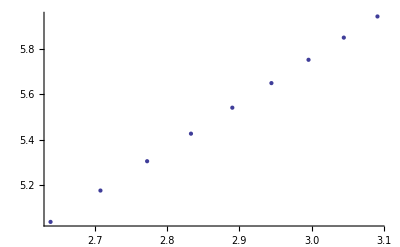

```mathematica
ListPlot[Table[{loglog[[i,1]],loglog[[i,2]]},{i,1,Length[loglog]}]]
```

Using w_i = 1/Δi^2, from Taylor.

```mathematica
weights=Table[1/(loglog[[i,3]]^2),{i,1,Length[loglog]}];
```

This is also from Taylor, used below

```mathematica
Delta=Sum[weights[[i]],{i,Length[weights]}]*Sum[weights[[i]]*loglog[[i,1]]^2,{i,Length[loglog]}]-(Sum[weights[[i]]*loglog[[i,1]],{i,Length[loglog]}])^2;
```

More symbols to make expressions less unweildy.

```mathematica
x[i_]:=loglog[[i,1]];
y[i_]:=loglog[[i,2]];
w[i_]:=weights[[i]];
```

Now, the fit coefficients (for line off form y = A + Bx):

```mathematica
A=1/Delta(Sum[w[i]*x[i]^2,{i,Length[loglog]}]*Sum[w[i]*y[i],{i,Length[loglog]}]-Sum[w[i]*x[i],{i,Length[loglog]}]*Sum[w[i]*x[i]*y[i],{i,Length[loglog]}])
```

-0.236325

```mathematica
B=1/Delta(Sum[w[i],{i,Length[loglog]}]*Sum[w[i]*x[i]*y[i],{i,Length[loglog]}]-Sum[w[i]*x[i],{i,Length[loglog]}]*Sum[w[i]*y[i],{i,Length[loglog]}])
```

1.99867

Again, not quite quadratic. We can plot both:

```mathematica
F[x_]:=A+B*x
```

```mathematica
Needs["ErrorBarPlots`"]
```

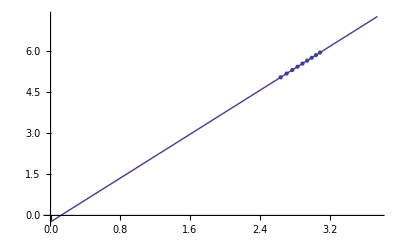

```mathematica
Show[Plot[F[x],{x,0,3.75}],ErrorListPlot[Table[{{x[i],y[i]},ErrorBar[loglog[[i,3]]]},{i,1,Length[loglog]}]]]
```

Uncertainties in A and B:

```mathematica
σA=Sqrt[Sum[w[i]*x[i]^2,{i,Length[loglog]}]/Delta]
```

0.00107457

```mathematica
σB=Sqrt[Sum[w[i],{i,Length[loglog]}]/Delta]
```

0.000377715

Checking the goodness of the fit:

```mathematica
fitvals=Table[F[loglog[[i,1]]],{i,1,Length[loglog]}];
```

```mathematica
residuals=Table[fitvals[[i]]-loglog[[i,2]],{i,1,Length[loglog]}];
```

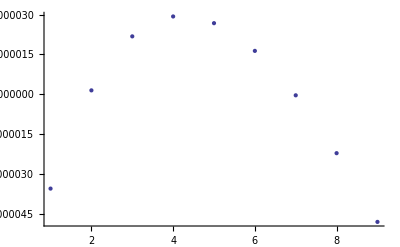

```mathematica
ListPlot[residuals]
```

This expression should output a list of booleans. TRUE means that the fit is inside the error bars (resdiual < error bar) and FALSE means it’s outside

```mathematica
Table[Abs[residuals[[i]]]<loglog[[i,3]],{i,1,Length[loglog]}]
```

{True,True,True,True,True,True,True,True,True}

Hey :(

Making sure nothing stupid happened:

```mathematica
fitvals
```

{5.03829,5.17618,5.30518,5.42634,5.54059,5.64865,5.75117,5.84868,5.94166}

```mathematica
Table[loglog[[i,2]],{i,1,Length[loglog]}]
```

{5.03833,5.17618,5.30515,5.42632,5.54056,5.64863,5.75117,5.8487,5.94171}

Not...that I can see :( :( :(

## Accuracy Check

```mathematica
data
```

{{0.841294,0.000678711},{3.22846,0.00198746},{7.18073,0.006917},{12.6891,0.000410257},{19.7731,0.000808489},{28.4267,0.00141043},{38.6504,0.00225641},{50.4443,0.00338957},{63.8087,0.00485306},{78.7438,0.00669285},{95.2497,0.0089535},{113.326,0.0116803},{132.974,0.0149213},{154.193,0.018724}}

```mathematica
evsfound
```

{{12.9004,13.8672},{19.668,20.6348},{28.3691,29.3359},{39.0039,39.9707},{50.6055,51.5723},{64.1406,65.1074},{78.6426,79.6094},{96.0449,97.0117},{113.447,114.414},{133.75,134.717},{155.02,155.986},{178.223,179.189},{202.393,203.359},{228.496,229.463},{255.566,256.533},{285.537,286.504},{315.508,316.475},{348.379,349.346},{382.217,383.184},{417.988,418.955},{454.727,455.693},{493.398,494.365},{533.037,534.004},{574.609,575.576},{618.115,619.082},{663.555,664.521},{709.961,710.928},{757.334,758.301},{807.607,808.574},{858.848,859.814},{911.055,912.021},{965.195,966.162}}